```mathematica
data={{{2014,7,31},{9.49,9.51,9.28,9.29,8.11727*^6}},{{2014,7,30},{9.49,9.61,9.45,9.52,2.7366988*^7}},{{2014,7,29},{9.4,9.5,9.32,9.41,1.8393449*^7}},{{2014,7,28},{9.48,9.51,9.3,9.38,1.5248228*^7}},{{2014,7,25},{9.41,9.52,9.4,9.45,2.4961717*^7}},{{2014,7,24},{9.18,9.44,9.13,9.42,3.2944941*^7}},{{2014,7,23},{9.1,9.25,9.08,9.2,2.2092388*^7}},{{2014,7,22},{8.99,9.2,8.94,9.14,4.6347911*^7}},{{2014,7,21},{8.95,8.98,8.86,8.92,1.3881668*^7}},{{2014,7,18},{8.94,8.99,8.88,8.97,2.2966311*^7}},{{2014,7,17},{9.11,9.13,8.96,9.,2.0671918*^7}},{{2014,7,16},{9.20,9.19,8.97,9.14,1.8464967*^7}},{{2014,7,15},{9.08,9.15,8.91,8.99,2.2118944*^7}},{{2014,7,14},{9.1,9.17,8.97,9.11,1.9952031*^7}},{{2014,7,11},{9.12,9.2,8.98,9.04,2.4544179*^7}}};
```

```mathematica
Length[data]
```

15

```mathematica
? Borsa`*
```

FDDates[FD] Returns the dates of the temporal series of financial data
	Input: Financial Data obtained from Yahoo, {date,{open,high,low,close,volume},...}
	Output: Dates, {{date},...}

```mathematica
?FDClose
```

FDClose[FD] Returns the temporal series of close prices
	Input: Financial Data obtained from Yahoo, {date,{open,high,low,close,volume},...}
	Output: Close prices, {{date,close},...}

```mathematica
ddata=depureData[data]
```

{{{2014,7,31},{9.49,9.51,9.28,9.29,8.11727×10^6}},{{2014,7,30},{9.49,9.61,9.45,9.52,2.7367×10^7}},{{2014,7,29},{9.4,9.5,9.32,9.41,1.83934×10^7}},{{2014,7,28},{9.48,9.51,9.3,9.38,1.52482×10^7}},{{2014,7,25},{9.41,9.52,9.4,9.45,2.49617×10^7}},{{2014,7,24},{9.18,9.44,9.13,9.42,3.29449×10^7}},{{2014,7,23},{9.1,9.25,9.08,9.2,2.20924×10^7}},{{2014,7,22},{8.99,9.2,8.94,9.14,4.63479×10^7}},{{2014,7,21},{8.95,8.98,8.86,8.92,1.38817×10^7}},{{2014,7,18},{8.94,8.99,8.88,8.97,2.29663×10^7}},{{2014,7,17},{9.11,9.13,8.96,9.,2.06719×10^7}},{{2014,7,15},{9.08,9.15,8.91,8.99,2.21189×10^7}},{{2014,7,14},{9.1,9.17,8.97,9.11,1.9952×10^7}},{{2014,7,11},{9.12,9.2,8.98,9.04,2.45442×10^7}}}

```mathematica
weekdata=WeekPrices[data]
```

{{{2014,7,28},{9.48,9.61,9.28,9.29,6.91259×10^7}},{{2014,7,21},{8.95,9.52,8.86,9.45,1.40229×10^8}},{{2014,7,14},{9.1,9.19,8.88,8.97,1.04174×10^8}},{{2014,7,11},{9.12,9.2,8.98,9.04,2.45442×10^7}}}

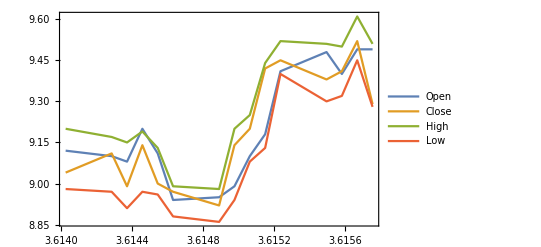

```mathematica
P1=DateListPlot[{FDOpen[data],FDClose[data],FDHigh[data],FDLow[data]},PlotLegends-> {"Open","Close","High","Low"}]
```

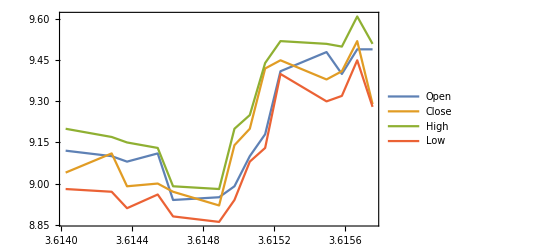

```mathematica
P2=DateListPlot[{FDOpen[ddata],FDClose[ddata],FDHigh[ddata],FDLow[ddata]},PlotLegends-> {"Open","Close","High","Low"}]
```

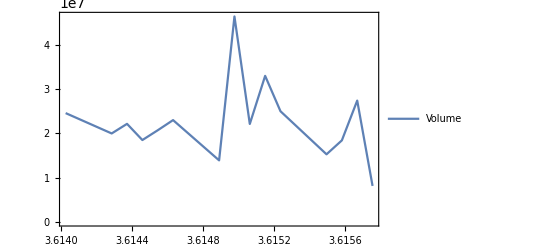

```mathematica
P3=DateListPlot[FDVolume[data],PlotLegends-> {"Volume"}]
```

```mathematica
Options[kNNForecast]
```

{Borsa`Private`Weighting→Mean,DistanceFunction→Automatic,Method→Automatic,WorkingPrecision→Automatic}

```mathematica
kNNForecast[FDClose[data][[All,2]],3,2,3]
```

{9.29,9.52,9.41,9.38,9.45,9.42,9.2,9.14,8.92,8.97,9.,9.14,8.99,9.11,9.04,9.04303,9.05767}

```mathematica
FDClose[data]
```

{{{2014,7,31},9.29},{{2014,7,30},9.52},{{2014,7,29},9.41},{{2014,7,28},9.38},{{2014,7,25},9.45},{{2014,7,24},9.42},{{2014,7,23},9.2},{{2014,7,22},9.14},{{2014,7,21},8.92},{{2014,7,18},8.97},{{2014,7,17},9.},{{2014,7,16},9.14},{{2014,7,15},8.99},{{2014,7,14},9.11},{{2014,7,11},9.04}}

```mathematica
EMA[n_,prices_]:=Module[{date,ema},
date=Map[#[[1]]&,prices];
ema=Reverse[ExponentialMovingAverage[Reverse[Map[#[[2]]&,FDClose[prices]]],2/(n+1)]];
{Transpose[{date,ema}]}
]
```

```mathematica
EMA[22,data]
```

{{{{2014,7,31},9.20206},{{2014,7,30},9.19368},{{2014,7,29},9.1626},{{2014,7,28},9.13904},{{2014,7,25},9.11609},{{2014,7,24},9.08429},{{2014,7,23},9.05232},{{2014,7,22},9.03826},{{2014,7,21},9.02857},{{2014,7,18},9.03891},{{2014,7,17},9.04547},{{2014,7,16},9.0498},{{2014,7,15},9.04121},{{2014,7,14},9.04609},{{2014,7,11},9.04}}}

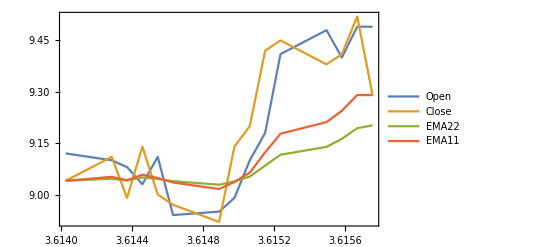

```mathematica
DateListPlot[{FDOpen[data],FDClose[data],EMA[22,data],EMA[11,data]},PlotLegends-> {"Open","Close","EMA22","EMA11"}]
```

```mathematica
InteractiveTradingChart[Reverse[data]]
```